# Project

Facial images convey many important human characteristics, such as identity, gender, expression, age, and ethnicity. 
Representative examples including face recognition, facial expression recognition, age estimation, gender classification and ethnicity recognition.

Objective:
Identify the kinship using faces.

Dataset:

Labeled faces in the Wild

Import data

```mathematica
data=Import[""]
```

import the code

```mathematica
<<Project`
```

```mathematica
?Classify
```

Classify[{example_1→class_1,example_2→class_2,…}] generates a ClassifierFunction[…] based on the examples and classes given.
Classify[{example_1,example_2,…}→{class_1,class_2,…}] also generates a ClassifierFunction[…] based on the examples and classes given.
Classify[<|class_1→{example_11,example_12,…},class_2→{example_21,…},…|>] generates a ClassifierFunction[…] based on an association of classes with their examples.
Classify[training,data] attempts to classify data using a classifier function deduced from the training set given.
Classify[name,data] attempts to classify data using the built-in classifier function represented by "name".
Classify[…,data,prop] gives the specified property of the classification associated with data.
Classify[classifier,opts] takes an existing classifier function and modifies it with the new options given.

```mathematica
ImageSize
```

```mathematica
MorphologicalComponents
```

```mathematica
ImageResize
```

```mathematica
ImageDimensions[-Graphics-]
```

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
ImageDimensions[-Graphics-]
```

{64,64}

```mathematica
FindFaces
```

```mathematica
FeatureExtraction
```

```mathematica
MorphologicalPerimeter
```

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son"]
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son

```mathematica
fatherSon=Import["fs*"];
```

```mathematica
dataFatherSon=Partition[fatherSon,2];
```

```mathematica
realFatherSon=Take[dataFatherSon,Length[dataFatherSon]/2];
```

```mathematica
fakeFatherSon=Take[dataFatherSon,-Length[dataFatherSon]/2];
```

```mathematica
fakeFatherSonRandom=Transpose[{RandomSample[Transpose[fakeFatherSon][[1]]],
RandomSample[Transpose[fakeFatherSon][[2]]]}];
```

```mathematica
cl=Classify@Flatten@MapThread[{#1->"RealFS",#2->"FakeFS"}&,{realFatherSon,fakeFatherSonRandom},]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,Flatten@MapThread[{#1->"RealFS",#2->"FakeFS"}&,{realFatherSon,fakeFatherSonRandom}]]
```

ClassifierMeasurementsObject[…]

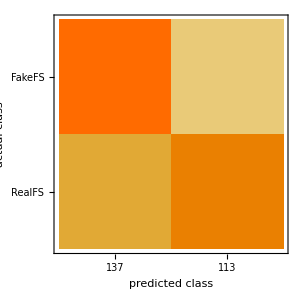

```mathematica
%["ConfusionMatrixPlot"]
```